Authors’ Institution @ Publication

```mathematica
First@integerYearBookWinnersSplitAuthors
```

<|Year→2017,Book Title→Juarez Girls Rising: Transformative Education in Times of Dystopia,Author→{Claudia G.Cervantes-Soon},Academic Acknowledgements→{Angela Valenzuela,Aurolyn Luykx,Carol Brochin,Cecilia Balli,Douglas E. Foley,Elaine Hampton,Elizabeth Villareal,G. Sue Kasun ,Haydee Rodriguez,Keffrelyn Brown,Lourdes Diaz Soto,Luis Urrieta,Monica Neshyba,Toni Avila},Authors' Institution @ Publication→UNC, Chapel Hill,Author UG→UT, El Paso,Author PhD→UT, Austin,Publisher→University of Minnesota|>

```mathematica
authorsAtPublication=integerYearBookWinners[[All,"Authors' Institution @ Publication"]];
```

```mathematica
authorsSplitAtPublication = integerYearBookWinnersSplitAuthors[[All,"Authors' Institution @ Publication"]];
```

```mathematica
MatchQ[authorsAtPublication==authorsSplitAtPublication]
```

MatchQ[True]

```mathematica
2+2.==4
```

True

```mathematica
MatchQ[authorsAtPublication===authorsSplitAtPublication]
```

MatchQ[True]

```mathematica
2+2.===4
```

False

The PieChart below was made by first generating the variable output (the first line) and then using the GUI functions, and the copying/pasting below the first function via suppression

```mathematica
authorsAtPublication;
Tally[%];
PieChart[Apply[Labeled,Reverse[%,2],{1}]]
```

-Graphics-

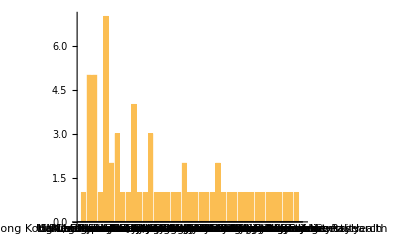

```mathematica
authorsAtPublication;
Tally[%];
BarChart[Apply[Labeled,Reverse[%,2],{1}]]
```